# PHY - 206 : HW 4

## RITA ABANI 19244

### QUESTION 1

### 1a)

Let us first solve the differential equation for the given function with the given initial condition.

```mathematica
T=DSolve[{x'[t]==-x[t]*t,x[0]==1},x[t],t]
```

{{x[t]→ⅇ^(-t^2/2)}}

```mathematica
ti=0;
tf=5;
xi=1;
nMax=200;
h=(tf-ti)/nMax//N;
f[t_,x_] =-x*t;
datalist={};
AppendTo[datalist,{ti,xi}];
xprev=xi;
tprev=ti;
```

```mathematica
For[n=1,n≤nMax,n++ , xnew=xprev+ h*f[tprev,xprev];
tnew=tprev+h;
AppendTo[datalist,{tnew,xnew}];
xprev=xnew;
tprev=tnew;]
```

```mathematica
datalist; dataplot=ListPlot[datalist]
funcplot=Plot[Exp[(-t*t)/2] , {t,0,5}]
Show[dataplot, funcplot]
```

-Graphics-

-Graphics-

-Graphics-

As can be seen from the above plot, the numerical and analytical solutions match.

### 1b)

```mathematica
ClearAll;
```

Let's first solve the differential equation

```mathematica
T=DSolve[{x'[t]==1-t,x[0]==0},x[t],t]
```

{{x[t]→1/2 (2 t-t^2)}}

```mathematica
ti=0;
tf=1;
xi=0;
nMax=200;
h=(tf-ti)/nMax//N;
f[t_,x_] =1-t;
datalist={};
AppendTo[datalist,{ti,xi}];
xprev=xi;
tprev=ti;
```

```mathematica
For[n=1,n≤nMax,n++ , xnew=xprev+ h*f[tprev,xprev];
tnew=tprev+h;
AppendTo[datalist,{tnew,xnew}];
xprev=xnew;
tprev=tnew;]
```

```mathematica
datalist; dataplot=ListPlot[datalist]
funcplot=Plot[t-((t^2)/2) , {t,0,1}]
Show[dataplot, funcplot]
```

-Graphics-

-Graphics-

-Graphics-

As can be seen from the above plot, the numerical and analytical solutions match.

### 1c)

Let's first solve the differential equation.

```mathematica
ClearAll;
```

```mathematica
T=DSolve[{x'[t]==Cos[t],x[Pi]==1},x[t],t]
```

{{x[t]→1+Sin[t]}}

```mathematica
ti=Pi;
tf=3*Pi;
xi=1;
nMax=200;
h=(tf-ti)/nMax//N;
f[t_,x_] =Cos[t];
datalist={};
AppendTo[datalist,{ti,xi}];
xprev=xi;
tprev=ti;
```

```mathematica
For[n=1,n≤nMax,n++ , xnew=xprev+ h*f[tprev,xprev];
tnew=tprev+h;
AppendTo[datalist,{tnew,xnew}];
xprev=xnew;
tprev=tnew;]
```

```mathematica
datalist; dataplot=ListPlot[datalist]
funcplot=Plot[1 + Sin[t] , {t,Pi,3*Pi}]
Show[dataplot, funcplot]
```

-Graphics-

-Graphics-

-Graphics-

As can be seen from the above plots, the numerical and analytical solutions match.

### 1d)

Let's first solve the differential equation

```mathematica
ClearAll;
```

```mathematica
T=DSolve[{x'[t]==(Sech[t])^2,x[1]==1},x[t],t]
```

{{x[t]→1-Tanh[1]+Tanh[t]}}

```mathematica
ti=-1;
tf=1;
xi=1;
nMax=1000;
h=(tf-ti)/nMax//N;
f[t_,x_] =(Sech[t])^2;
datalist={};
AppendTo[datalist,{ti,xi}];
xprev=xi;
tprev=ti;
```

```mathematica
For[n=1,n≤nMax,n++ , xnew=xprev+ h*f[tprev,xprev];
tnew=tprev+h;
AppendTo[datalist,{tnew,xnew}];
xprev=xnew;
tprev=tnew;]
```

1-Tanh[1] = 0.238406

```mathematica
datalist; dataplot=ListPlot[datalist]
funcplot=Plot[(0.23840584 + Tanh[t]) , {t,-1,1}]

Show[dataplot, funcplot]
```

-Graphics-

-Graphics-

-Graphics-

As can be seen from the above plot, the numerical and analytical solutions slightly differ.

### Question 2

#### a)

We have been given the differential equation x'(t) = x^2 - t^2

We need to solve the above equation using Euler's method.

```mathematica
ClearAll;
```

```mathematica
ti=0;
tf=1;
xi=1;
nMax=200;
h=(tf-ti)/nMax//N;
f[t_,x_] =x^2 - t^2;
datalist={};
AppendTo[datalist,{ti,xi}];
xprev=xi;
tprev=ti;
```

```mathematica
For[n=1,n≤nMax,n++ , xnew=xprev+ h*f[tprev,xprev];
tnew=tprev+h;
AppendTo[datalist,{tnew,xnew}];
xprev=xnew;
tprev=tnew;]
```

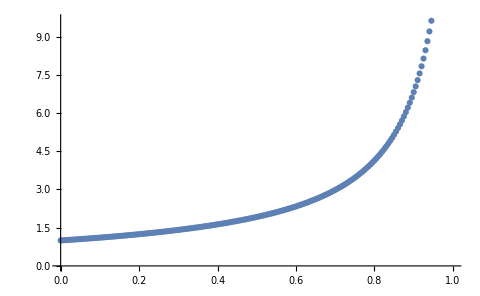

```mathematica
datalist; dataplot=ListPlot[datalist]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
T=DSolve[{x'[t]==x[t]^2-t^2,x[0]==1},x[t],t]
```

{{x[t]→((1/2+ⅈ/2) ((-1-ⅈ) t^2 BesselJ[-3/4,(ⅈ t^2)/2] Gamma[1/4]+ⅈ √2 t^2 BesselJ[-5/4,(ⅈ t^2)/2] Gamma[3/4]+√2 BesselJ[-1/4,(ⅈ t^2)/2] Gamma[3/4]-ⅈ √2 t^2 BesselJ[3/4,(ⅈ t^2)/2] Gamma[3/4]))/(t (BesselJ[1/4,(ⅈ t^2)/2] Gamma[1/4]-(1+ⅈ) √2 BesselJ[-1/4,(ⅈ t^2)/2] Gamma[3/4]))}}

### b)

```mathematica
ClearAll;
```

```mathematica
ti=0;
tf=1;
xi=0.5;
nMax=200;
h=(tf-ti)/nMax//N;
f[t_,x_] =x^2 - t^2;
datalist={};
AppendTo[datalist,{ti,xi}];
xprev=xi;
tprev=ti;
```

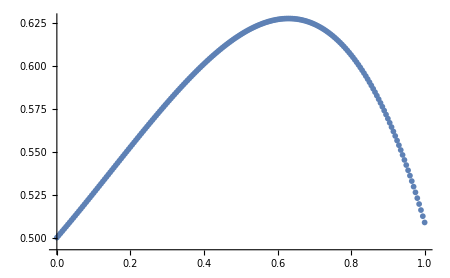

```mathematica
For[n=1,n≤nMax,n++ , xnew=xprev+ h*f[tprev,xprev];
tnew=tprev+h;
AppendTo[datalist,{tnew,xnew}];
xprev=xnew;
tprev=tnew;]
datalist; dataplot=ListPlot[datalist]
```

### c)

```mathematica
ClearAll;
```

```mathematica
ti=0;
tf=1;
xi=0;
nMax=200;
h=(tf-ti)/nMax//N;
f[t_,x_] =x^2 - t^2;
datalist={};
AppendTo[datalist,{ti,xi}];
xprev=xi;
tprev=ti;
```

```mathematica
For[n=1,n≤nMax,n++ , xnew=xprev+ h*f[tprev,xprev];
tnew=tprev+h;
AppendTo[datalist,{tnew,xnew}];
xprev=xnew;
tprev=tnew;]
datalist; dataplot=ListPlot[datalist]
```

-Graphics-

### d)

```mathematica
ClearAll;
```

```mathematica
ti=0;
tf=1;
xi=-1;
nMax=200;
h=(tf-ti)/nMax//N;
f[t_,x_] =x^2 - t^2;
datalist={};
AppendTo[datalist,{ti,xi}];
xprev=xi;
tprev=ti;
```

```mathematica
For[n=1,n≤nMax,n++ , xnew=xprev+ h*f[tprev,xprev];
tnew=tprev+h;
AppendTo[datalist,{tnew,xnew}];
xprev=xnew;
tprev=tnew;]
datalist; dataplot=ListPlot[datalist]
```

-Graphics-